#### Classical Sigmoid function

Wikipedia 
https://www.wikiwand.com/en/Sigmoid_function

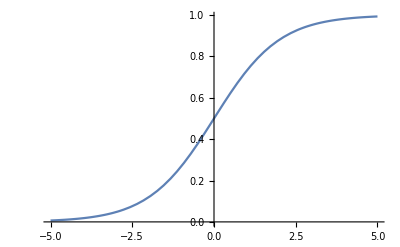

```mathematica
Z[x_]:=1/(ⅇ^-x+1)
Plot[Z[x],{x,-5,5}]
```

```mathematica
Lin[x_, k_, n_] := (k*(0.5*n - x))/n; 
Manipulate[Plot[Lin[x, k, n], {x, 0, n}], 
  {n, 10, 1000, Appearance -> "Labeled"}, 
  {k, 5, 20, Appearance -> "Labeled"}]
```

```mathematica
Manipulate[Plot[Zigmoid@ Lin[x,k,n],{x,0,n}],{n,10,1000,Appearance->"Labeled"},{k,5,40,Appearance->"Labeled"}]
```

#### Modified Sigmoid

```mathematica
Manipulate[Plot[1-1/(ⅇ^((k (0.5 n-x))/n)+1),{x,0,n}],{n,10,1000,Appearance->"Labeled"},{k,5,20,Appearance->"Labeled"}]
```